## Perimeter-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m;
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Sat 10 Nov 2012 08:51:08
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
```

```mathematica
Perimeter[polygon]
```

4.18945

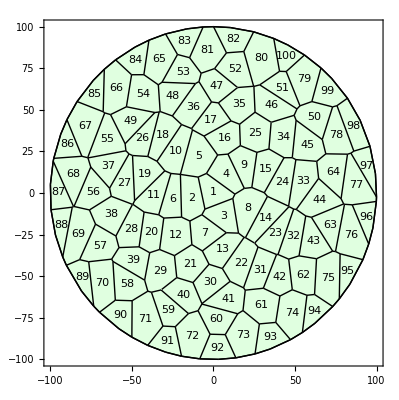

```mathematica
w=TemplateRandomCircularGrid[100,100];
ShowTissue[w,"CellNumbers"->True, Frame-> True]
```

```mathematica
Perimeter[w,1]
```

67.7775

```mathematica
perimeters=Perimeter[w]
```

{67.7775,74.1452,69.169,70.4104,79.4507,72.0992,66.8059,79.9222,68.9688,79.4055,75.6136,72.1663,70.5663,79.7588,72.2053,66.9972,65.565,76.9455,76.1034,66.7052,67.4391,77.7107,78.7957,77.3295,70.9949,75.1149,74.8236,70.7905,73.6995,68.0175,73.0665,75.6215,79.814,72.313,71.3399,75.3295,73.0677,74.8587,68.8321,69.3134,71.7958,68.0289,73.811,76.9884,73.7902,76.745,65.6553,71.3355,74.4362,71.2504,70.6376,72.327,66.7274,74.9701,80.3871,73.328,73.1556,74.2546,68.453,67.2859,73.6366,71.8111,76.774,76.1941,78.835,82.9565,87.2261,84.7275,88.3851,83.1379,82.6751,78.8674,76.915,78.8529,83.7704,86.903,86.2998,79.0958,78.6802,86.519,76.6043,66.436,65.6516,65.4188,68.3038,65.7675,73.2813,72.9624,71.2231,69.192,62.3884,62.9765,65.4761,64.8195,69.247,66.6603,73.9032,79.4715,69.0918,60.444}

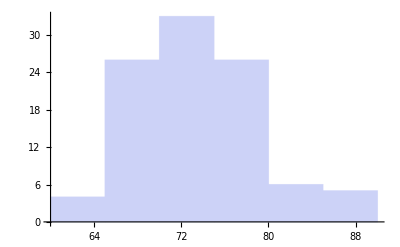

```mathematica
Histogram[Perimeter[w]]
```

```mathematica
areas=Area[w]
```

{264.143,325.106,275.657,292.942,389.492,265.577,285.712,380.538,277.082,346.384,299.275,359.08,301.704,302.583,309.045,299.146,259.725,309.664,308.997,275.206,321.475,356.398,286.655,321.199,355.833,275.031,282.245,293.703,375.732,292.813,291.944,294.509,343.647,325.54,342.9,341.272,292.022,359.863,290.926,306.598,302.551,287.055,304.265,348.679,331.269,347.451,282.164,291.387,301.451,319.778,253.058,326.736,271.68,365.867,344.075,313.03,339.279,320.713,270.55,274.983,377.263,331.466,287.041,337.672,399.467,425.296,441.93,383.843,430.624,395.93,434.746,418.142,398.862,408.322,418.54,422.472,392.491,341.056,388.96,482.954,392.231,251.216,241.355,235.4,216.137,204.112,217.819,205.953,216.436,266.15,223.527,232.877,248.554,214.071,202.978,195.037,207.632,294.526,274.491,195.328}

Calculate an isoperimetric ratio A/L^2; for a circle, 1/4Pi = 0.0796; for a square, 1/16=0.0625; according to the isoperimetric inequality, A/L^2 <= 4Pi

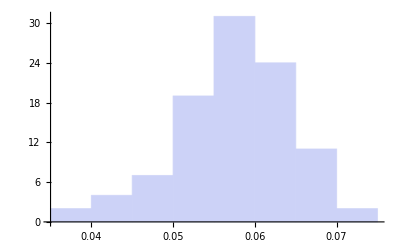

```mathematica
Histogram[areas/perimeters^2]
```